# AAS Data Analysis and Calibration

```mathematica
pbStds=ImportString["0.857\t0.0104
8.57\t0.0927
85.7\t0.7127
0.857\t0.0108
8.57\t0.0923
85.7\t0.7156", "Data"];
pbStds // Grid
```

0.857 | 0.0104
8.57 | 0.0927
85.7 | 0.7127
0.857 | 0.0108
8.57 | 0.0923
85.7 | 0.7156

```mathematica
cuStds=ImportString["1.19\t0.086
5.95\t0.4109
59.5\t1.8943
1.19\t0.0868
5.95\t0.4085
59.5\t1.8876
1.19\t0.0865", "Data"]
cuStds//Grid
```

{{1.19,0.086},{5.95,0.4109},{59.5,1.8943},{1.19,0.0868},{5.95,0.4085},{59.5,1.8876},{1.19,0.0865}}

1.19 | 0.086
5.95 | 0.4109
59.5 | 1.8943
1.19 | 0.0868
5.95 | 0.4085
59.5 | 1.8876
1.19 | 0.0865

```mathematica
feStds=ImportString["1\t0.0035
10\t0.2595
100\t1.1551
1\t0.0031
10\t0.2702
100\t1.1588
1\t0.0016", "Data"]
feStds//Grid
```

{{1,0.0035},{10,0.2595},{100,1.1551},{1,0.0031},{10,0.2702},{100,1.1588},{1,0.0016}}

1 | 0.0035
10 | 0.2595
100 | 1.1551
1 | 0.0031
10 | 0.2702
100 | 1.1588
1 | 0.0016

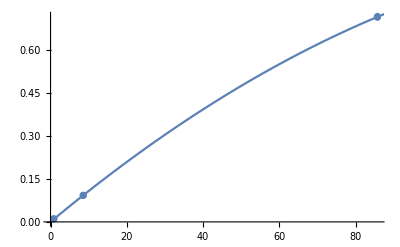

```mathematica
Show[ListPlot[pbStds], Plot[nlm,{conc, 0, 90}]]
```

```mathematica
fit[data_]:=Module[{model, nlm,plt},
model[conc_]:=d conc^3+a conc^2 + b conc + c;
constraint = model[0]==0;
nlm=NonlinearModelFit[data, {model[conc], constraint},{a,b,c,d},conc]//Normal;
(*Print[nlm];*)
plt=Show[ListPlot[data], Plot[nlm,{conc, 0, 90}]];
Print[plt];
nlm
]
```

```mathematica
fit[pbStds]
```

-Graphics-

0.+0.0110829 conc-0.0000320859 conc^2

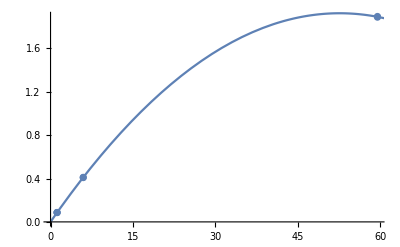

0.+0.0731315 conc-0.000694975 conc^2

```mathematica
fit[cuStds]
```

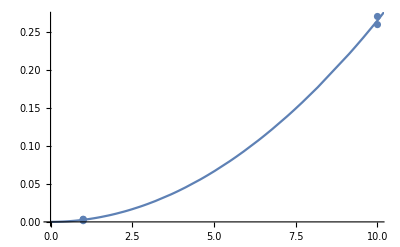

0.+0.0000942601 conc+0.00263907 conc^2

```mathematica
fit[Cases[feStds,{abs_,_}/;abs<50]]
```